```mathematica
Graphics3D[
{
RGBColor[0,0,1,0.6],
Simplex[
{
{0.7,0.3,0},{0,1,0},{0,0.3,0.7}
}
],
RGBColor[0,0,1,0.3],
Simplex[
{
{1,0,0},{0,1,0},{0,0,1}
}
],
RGBColor[0,0,0,0.8],
Thick,
Arrow[{{0,1,0},{0,0.3,0}}],
Arrow[{{0.7,0.3,0},{0,0.3,0}}],
Arrow[{{0,0.3,0.7},{0,0.3,0}}],
RGBColor[1,0,0],
Ball[{0,0.3,0},0.02]
},
PlotRange->{{-0.1,1},{-0.1,1},{-0.1,1}},
Axes->True
]
```

-Graphics3D-

```mathematica
Graphics3D[
{
RGBColor[0.1,0.7,0.9,0.5],
Simplex[
{{1,0,0},{0,1,0},{0,0,1}}
],
RGBColor[0,0.3,0.9,0.8],
Ball[{1,0,0},0.02],
Ball[{0,1,0},0.02],
Ball[{0,0,1},0.02],
Ball[{1/3,1/3,1/3},0.02],
Ball[{1/3,2/3,0},0.02],
Ball[{1/3,0,2/3},0.02],
Ball[{2/3,1/3,0},0.02],
Ball[{0,1/3,2/3},0.02],
Ball[{2/3,0,1/3},0.02],
Ball[{0,2/3,1/3},0.02]
},
Axes->True
]
```

-Graphics3D-

```mathematica
Graphics3D[
{
RGBColor[0.9,0.3,0.3,0.5],
Simplex[
{{1,0,0},{0,1,0},{0,0,1}}
],
RGBColor[0.1,0.7,0.9,0.6],
Simplex[
{{5/6,1/6,0},{0,1,0},{0,1/6,5/6}}
],
RGBColor[0,0.3,0.9,0.8],
Ball[{0,1,0},0.02],
Ball[{1/3,1/3,1/3},0.02],
Ball[{1/3,2/3,0},0.02],
Ball[{2/3,1/3,0},0.02],
Ball[{0,1/3,2/3},0.02],
Ball[{0,2/3,1/3},0.02],
RGBColor[0.9,0.3,0.3,0.8],
Ball[{1,0,0},0.02],
Ball[{0,0,1},0.02],
Ball[{1/3,0,2/3},0.02],
Ball[{2/3,0,1/3},0.02],
},
Axes->True
]
```

-Graphics3D-

```mathematica
Plot3D[
Min[0, 15 * ((x - 3/4)^2 +(y - 1/4)^2 )] - 4 
+ Min[0, 15 * ((x -1/4)^2 +(y - 3/4)^2 ) - 2], 
{x,0,1},
{y, 0, 1}
]
```

-Graphics3D-

```mathematica
Needs["TetGenLink`"]
{points, surface} = TetGenConvexHull[
{
{0, 0, 0},
{1, 0, 0},
{1/2, 0, Sqrt[3]/2},
{1/2, Sqrt[2/3], 1 / (2 * Sqrt[3])}
}
]
Graphics3D[
{
RGBColor[0.1,0.8,0.9,0.2],
GraphicsComplex[
points,
Polygon[surface]
],
RGBColor[0,0.2,0.9,0.8],
Ball[{1/2,Sqrt[2] / Sqrt[3],1/(2 * Sqrt[3])},0.02],(* vertex *)
Ball[{0,0,0},0.02],(* vertex *)
Ball[{1/2,0,Sqrt[3]/2},0.02],(* vertex *)
Ball[{1,0,0},0.02],(* vertex *)
Ball[{1/4, 1/Sqrt[6], 1/(4 * Sqrt[3])}, 0.02],
Ball[{1/4, 0, Sqrt[3]/4}, 0.02],
Ball[{1/2, 0, 0}, 0.02],
Ball[{3/4, 1/Sqrt[6], 1/(4*Sqrt[3])}, 0.02],
Ball[{1/2, 1/Sqrt[6], 1/Sqrt[3]}, 0.02],
Ball[{3/4, 0, Sqrt[3]/ 4}, 0.02]
},
Boxed->False
]
```

{{{0.,0.,0.},{1.,0.,0.},{0.5,0.,0.866025},{0.5,0.816497,0.288675}},{{2,1,3},{2,4,1},{1,4,3},{3,4,2}}}

-Graphics3D-

```mathematica
Needs["TetGenLink`"]
{points1, surface1} = TetGenConvexHull[
{
{0, 0, 0},
{1, 0, 0},
{1/2, 0, Sqrt[3]/2},
{1/2, Sqrt[2/3], 1 / (2 * Sqrt[3])}
}
]
{points2, surface2} = TetGenConvexHull[
{
{1/2, Sqrt[2/3], 1/(2 * Sqrt[3])},
{1/8,Sqrt[2]/(4 * Sqrt[3]), 1/(8*Sqrt[3])},
{1/2,Sqrt[2]/(4 * Sqrt[3]), 5/(4*Sqrt[3])},
{7/8,Sqrt[2]/(4 * Sqrt[3]), 1/(8*Sqrt[3])}
}
]
g1 = Graphics3D[
{
RGBColor[0.1,0.8,0.9,0.3],
GraphicsComplex[
points1,
Polygon[surface1]
],
RGBColor[0.1,0.8,0.9,0.8],
Ball[{0,0,0},0.02],(* vertex *)
Ball[{1,0,0},0.02],(* vertex *)
Ball[{1/2,0,Sqrt[3]/2},0.02],(* vertex *)
Ball[{1/4, 0, Sqrt[3]/4}, 0.02],
Ball[{1/2, 0, 0}, 0.02],
Ball[{3/4, 0, Sqrt[3]/ 4}, 0.02]
},
Boxed->False
]
g2 = Graphics3D[
{
Specularity[0,100],
RGBColor[0,0.2,0.9,0.4],
GraphicsComplex[
points2,
Polygon[surface2]
],
RGBColor[0,0.2,0.9,0.8],
Ball[{1/2,Sqrt[2] / Sqrt[3],1/(2 * Sqrt[3])},0.02],(* vertex *)
Ball[{1/4, 1/Sqrt[6], 1/(4 * Sqrt[3])}, 0.02],
Ball[{3/4, 1/Sqrt[6], 1/(4*Sqrt[3])}, 0.02],
Ball[{1/2, 1/Sqrt[6], 1/Sqrt[3]}, 0.02]
},
Boxed->False
]
Show[g1, g2]
```

{{{0.,0.,0.},{1.,0.,0.},{0.5,0.,0.866025},{0.5,0.816497,0.288675}},{{2,1,3},{2,4,1},{1,4,3},{3,4,2}}}

{{{0.5,0.816497,0.288675},{0.125,0.204124,0.0721688},{0.5,0.204124,0.721688},{0.875,0.204124,0.0721688}},{{2,1,3},{2,4,1},{1,4,3},{3,4,2}}}

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Graphics3D[
{
RGBColor[0.1,0.1,0.8, 0.6],
Simplex[
{
{0.5,0.2,0.3},{0.1,0.6,0.3},{0.1,0.2,0.7}
}
],
RGBColor[0,0,1,0.3],
Simplex[
{
{1,0,0},{0,1,0},{0,0,1}
}
],
RGBColor[0,0,0,0.8],
Thick,
Arrow[{{0.1,0.2,0.3},{0.5,0.2,0.3}}],
Arrow[{{0.1,0.2,0.3},{0.1,0.6,0.3}}],
Arrow[{{0.1,0.2,0.3},{0.1,0.2,0.7}}],
RGBColor[1,0,0],
Ball[{0.1,0.2,0.3},0.02]
},
PlotRange->{{0,1},{0,1},{0,1}},
Axes->True
]
```

-Graphics3D-

```mathematica
Graphics3D[
{
RGBColor[0.1,0.1,0.8, 0.6],
Simplex[
{
{0.5,0.2,0.3},{0.1,0.6,0.3},{0.1,0.2,0.7}
}
],
RGBColor[0,0,1,0.3],
Simplex[
{
{1,0,0},{0,1,0},{0,0,1}
}
],
RGBColor[0,0,0,0.8],
Thick,
Arrow[{{0.5,0.2,0.3},{0.1,0.2,0.3}}],
Arrow[{{0.1,0.6,0.3},{0.1,0.2,0.3}}],
Arrow[{{0.1,0.2,0.7},{0.1,0.2,0.3}}],
RGBColor[1,0,0],
Ball[{0.1,0.2,0.3},0.02]
},
PlotRange->{{0,1},{0,1},{0,1}},
Axes->True
]
```

-Graphics3D-

```mathematica
Plot3D[
Max[2.5x, 3y]+ Min[9x,8y], 
{x,0,1},
{y,0,1}
]
```

-Graphics3D-

```mathematica
Graphics3D[
{
RGBColor[0.1,0.7,0.9,0.7],
Simplex[
{{1,0,0},{0,1,0},{0,0,1}}
]
}
]
```

-Graphics3D-

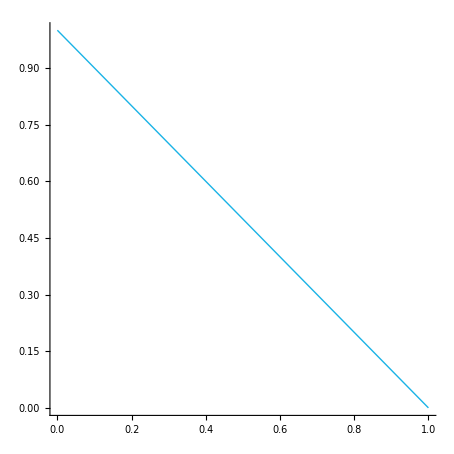

```mathematica
Graphics[
{
RGBColor[0.1,0.7,0.9],
Simplex[
{{1,0},{0,1}}
]
},
Axes->True
]
```

```mathematica
Needs["TetGenLink`"]
{points1, surface1} = TetGenConvexHull[
{
{0, 0, 0},
{1, 0, 0},
{1/2, 0, Sqrt[3]/2},
{1/2, Sqrt[2/3], 1 / (2 * Sqrt[3])}
}
]
g1 = Graphics3D[
{
RGBColor[0.1,0.7,0.9,0.7],
GraphicsComplex[
points1,
Polygon[surface1]
]
},
Boxed->False
]
```

{{{0.,0.,0.},{1.,0.,0.},{0.5,0.,0.866025},{0.5,0.816497,0.288675}},{{2,1,3},{2,4,1},{1,4,3},{3,4,2}}}

-Graphics3D-

```mathematica
Plot3D[
10*2+x^2-10Cos[2 * Pi * x]+y^2-10Cos[2 * Pi * y], 
{x,-5,5},
{y,-5,5}
]
```

-Graphics3D-

```mathematica
Plot3D[
(Sin[3*Pi*x])^2
+(x-1)^2*(1+(Sin[3*Pi*y])^2)
+(y-1)^2*(1+(Sin[2*Pi*y])^2), 
{x,-5,5},
{y,-5,5}
]
```

-Graphics3D-